PRVA NALOGA

```mathematica
trikotnik={{1,5},{3,7},{5,10}};
```

{{{5,10},{1,5},{3,7}},{{1,5},{3,7},{5,10}},{{3,7},{5,10},{1,5}}}

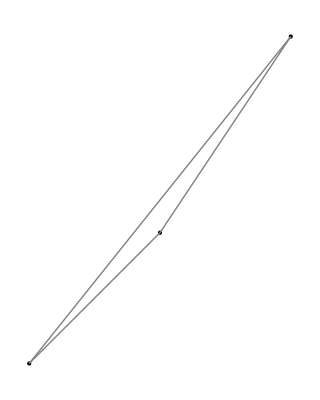

```mathematica
Stranice[{AA_,BB_,CC_}]:= {{AA,BB},{BB,CC},{CC,AA}} 
(*"Stranice" podajo kateri pari točk sestavljajo katero stranico*)
Koti[{AA_,BB_,CC_}]:= {{CC,AA,BB},{AA,BB,CC},{BB,CC,AA}}
(*"Koti" povejo katere točke sestavljajo kot. Kot bo pri srednji vrednosti v trojici točk.*)
Koti[trikotnik]

SlikaOglisc[trikotnik_]:= Map[Point, trikotnik];
(*"SlikaOglisc" nariše podane točke*)
SlikaStranic[trikotnik_]:=Map[Line, Stranice[trikotnik]]
(*"SlikaStranic" potegne črto med točkami*)
NarisiTrikotnik[trikotnik_]:=Graphics[
{PointSize[Large],
SlikaOglisc[trikotnik], 
{Gray,SlikaStranic[trikotnik]}
}, 
AspectRatio->Automatic]
(*"NarisiTrikotnik" sedaj grafično pokaže vse kar smo s prejšnjimi funkcijami že podali. Torej grafično prikaže točke in črte ki jih izriše.*)
NarisiTrikotnik[trikotnik]
```

```mathematica
DRUGA NALOGA
```

DRUGA NALOGA

```mathematica
VektorSimetraleKota[{x_,y_,z_}] :=Normalize[Normalize[x-y]+Normalize[z-y]]
(*"VektorSimetraleKota" nardi enotske vektorje  iz vrednosti x,y,z, ki jih podamo. To je samo formula kako to dobimo enotske vektorje, če npr. vstavimo prejšnje točke trikotnika. Določi njihovo dolžino = 1
Programu definiramo kaj je za nas simetrala kota*)

SimetralaKota[{x_,y_,z_}, dol_:10]:={y,y+VektorSimetraleKota[{x,y,z}]*dol}
(*"SimetralaKota" definira kako bomo to simetralo prikazali. Podamo začetno točko, in ji prištejemo njen usmerjen vektor ki smo ga dobili pri VektorSimetraleKota. Vektorsimetralekota podaljšamo za 10.*)

(* y=kx+n*)

SimetralaKota[trikotnik]
```

{{3,7},{3+(10 (-1/(√2)+2/(√13)))/(√((1/(√2)-2/(√13))^2+(-1/(√2)+3/(√13))^2)),7+(10 (-1/(√2)+3/(√13)))/(√((1/(√2)-2/(√13))^2+(-1/(√2)+3/(√13))^2))}}

```mathematica
Koti[trikotnik]
SlikaSimetralKotov[trikotnik]
```

{{{5,10},{1,5},{3,7}},{{1,5},{3,7},{5,10}},{{3,7},{5,10},{1,5}}}

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

General::stop: Further output of Normalize::nlnmt2 will be suppressed during this calculation.

-Graphics-

TRETJA NALOGA

```mathematica
ClearAll[SlikaSimetralKotov]
```

```mathematica
SlikaSimetralKotov[trikotnik_]:=Map[Line,Map[SimetralaKota,Koti[trikotnik]]] 
(*"SlikaSimetralKotov" "mapira" oz prikaže kar smo prej definirali, vendar to izrišemo šele z ukazom Graphics. Se pravi, programu povemo, (če začnemo iz najbolj notranjega izraza) da naj mapira SimetraleKotov, z parametrom Koti[trikotnik]. Prav tako mu povemo da naj naredi tudi črti, med mapiranami točkami. Zunanji Map poveže Line in notranji Map.*)
Map[Line,Map[SimetralaKota,Koti[trikotnik]]] 
SlikaSimetralKotov[trikotnik]
Map[SimetralaKota,Koti[trikotnik]]
```

{Line[{{1,5},{1+(10 (1/(√2)+4/(√41)))/(√((1/(√2)+4/(√41))^2+(1/(√2)+5/(√41))^2)),5+(10 (1/(√2)+5/(√41)))/(√((1/(√2)+4/(√41))^2+(1/(√2)+5/(√41))^2))}}],Line[{{3,7},{3+(10 (-1/(√2)+2/(√13)))/(√((1/(√2)-2/(√13))^2+(-1/(√2)+3/(√13))^2)),7+(10 (-1/(√2)+3/(√13)))/(√((1/(√2)-2/(√13))^2+(-1/(√2)+3/(√13))^2))}}],Line[{{5,10},{5+(10 (-2/(√13)-4/(√41)))/(√((2/(√13)+4/(√41))^2+(3/(√13)+5/(√41))^2)),10+(10 (-3/(√13)-5/(√41)))/(√((2/(√13)+4/(√41))^2+(3/(√13)+5/(√41))^2))}}]}

{Line[{{1,5},{1+(10 (1/(√2)+4/(√41)))/(√((1/(√2)+4/(√41))^2+(1/(√2)+5/(√41))^2)),5+(10 (1/(√2)+5/(√41)))/(√((1/(√2)+4/(√41))^2+(1/(√2)+5/(√41))^2))}}],Line[{{3,7},{3+(10 (-1/(√2)+2/(√13)))/(√((1/(√2)-2/(√13))^2+(-1/(√2)+3/(√13))^2)),7+(10 (-1/(√2)+3/(√13)))/(√((1/(√2)-2/(√13))^2+(-1/(√2)+3/(√13))^2))}}],Line[{{5,10},{5+(10 (-2/(√13)-4/(√41)))/(√((2/(√13)+4/(√41))^2+(3/(√13)+5/(√41))^2)),10+(10 (-3/(√13)-5/(√41)))/(√((2/(√13)+4/(√41))^2+(3/(√13)+5/(√41))^2))}}]}

{{{1,5},{1+(10 (1/(√2)+4/(√41)))/(√((1/(√2)+4/(√41))^2+(1/(√2)+5/(√41))^2)),5+(10 (1/(√2)+5/(√41)))/(√((1/(√2)+4/(√41))^2+(1/(√2)+5/(√41))^2))}},{{3,7},{3+(10 (-1/(√2)+2/(√13)))/(√((1/(√2)-2/(√13))^2+(-1/(√2)+3/(√13))^2)),7+(10 (-1/(√2)+3/(√13)))/(√((1/(√2)-2/(√13))^2+(-1/(√2)+3/(√13))^2))}},{{5,10},{5+(10 (-2/(√13)-4/(√41)))/(√((2/(√13)+4/(√41))^2+(3/(√13)+5/(√41))^2)),10+(10 (-3/(√13)-5/(√41)))/(√((2/(√13)+4/(√41))^2+(3/(√13)+5/(√41))^2))}}}

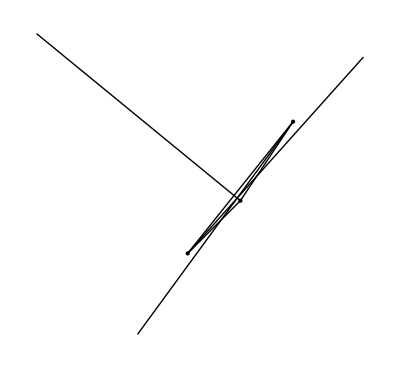

Function[trikotnik,Module[{slike},slike={SlikaOglisc[trikotnik],SlikaStranic[trikotnik],SlikaSimetralKotov[trikotnik]};-Graphics-]]

```mathematica
NarisiTrikotnik[trikotnik_]:= Module[{slike},
slike = {SlikaOglisc[trikotnik],SlikaStranic[trikotnik], SlikaSimetralKotov[trikotnik]};
Graphics[slike, AspectRatio->Full]
]

NarisiTrikotnik[trikotnik]
```